```mathematica
gU[r_,theta_]={{1/r^2,0},{0,1/(r*Sin[theta])^2}};
gL[r_,theta_]={{r^2,0},{0,(r*Sin[theta])^2}};
lc[r_,theta_]={{0, √Det[gL[r,theta]] },{-√Det[gL[r,theta]],0}};
lc3[r_,theta_]=LeviCivitaTensor[3]*r^2*Sin[theta];
gL3[r_,theta_]={{1,0,0},{0,r^2,0},{0,0,(r*Sin[theta])^2}};
gU3[r_,theta_]=Inverse[gL3[r,theta]];
```

```mathematica
lc[r,theta].Inverse[lc[r,theta]]
```

{{1,0},{0,1}}

# Mass

```mathematica
I4tt[red_, theta_, phi_,M_,a_,Ω_] = M*a^2*Ω^4(1+(Cos[theta])^2)Cos[2(phi-Ω(red))];
I4tp[red_, theta_, phi_,M_,a_,Ω_] =-2M*a^2*Ω^4 Cos[theta]Sin[2(phi-Ω(red))];
I4Mat[red_, theta_, phi_,M_,a_,Ω_]={{I4tt[red, theta, phi,M,a,Ω],I4tp[red, theta, phi,M,a,Ω] },
{I4tp[red, theta, phi,M,a,Ω],-I4tt[red, theta, phi,M,a,Ω]}};
```

## Electric Mass

```mathematica
ElectricQuadM[t_,r_, theta_, phi_,M_,Ω_]=-1/(2r)Table[I4Mat[t-r, theta, phi,M,1,Ω][[a]][[b]]+Sum[Sum[lc[r,theta][[a]][[c]]*I4Mat[t-r, theta, phi,M,1,Ω][[c]][[d]]*lc[r,theta][[d]][[b]],{d,1,2}],{c,1,2}],{a,1,2}, {b,1,2}] ;
```

## Magnetic Mass

```mathematica
MagneticQuadM[t_,r_,theta_,phi_,M_,Ω_]=-1/(2 r)Table[Sum[lc[r,theta][[c]][[a]]*I4Mat[t-r, theta, phi,M,1,Ω][[b]][[c]]+lc[r,theta][[c]][[b]]*I4Mat[t-r, theta, phi,M,1,Ω][[a]][[c]],{c,1,2}],{a,1,2},{b,1,2}];
```

## Magnetic Current

```mathematica
MagneticQuadC[C_,t_,r_, theta_, phi_,M_,Ω_,w_]=-C/(2r)Table[I4Mat[t-r, theta, phi-w,M,1,Ω][[a]][[b]]+Sum[Sum[lc[r,theta][[a]][[c]]*(4/3)*I4Mat[t-r, theta, phi-w,M,1,Ω][[c]][[d]]*lc[r,theta][[d]][[b]],{d,1,2}],{c,1,2}],{a,1,2}, {b,1,2}] ;
```

## Electric Current

```mathematica
ElectricQuadC[C_,t_,r_,theta_,phi_,M_,Ω_,w_]=-C/(2 r)Table[Sum[lc[r,theta][[c]][[a]]*(-4/3)*I4Mat[t-r, theta, phi-w,M,1,Ω][[b]][[c]]+lc[r,theta][[c]][[b]]*(-3/4)*I4Mat[t-r, theta, phi-w,M,1,Ω][[a]][[c]],{c,1,2}],{a,1,2},{b,1,2}];
```

# Octopole

```mathematica
S5tt[red_, theta_, phi_,M_,a_,Ω_,v_]=-(M*a^3*v*Ω^5)/24(5Cos[theta]+3Cos[3theta])Sin[2(phi-Ω*red)];
S5tp[red_, theta_, phi_,M_,a_,Ω_,v_]=-(M*a^3*v*Ω^5)/3 Cos[2theta]Cos[2(phi-Ω*red)];
S5Mat[red_, theta_, phi_,M_,a_,Ω_,v_]={{S5tt[red,theta,phi,M,a,Ω,v],S5tp[red,theta,phi,M,a,Ω,v]},{S5tp[red,theta,phi,M,a,Ω,v],-S5tt[red,theta,phi,M,a,Ω,v]}};
```

```mathematica
ElectricOctoC[t_,r_,theta_,phi_,M_,Ω_,v_]=1/(2r)Table[Sum[lc[r,theta][[c]][[a]]*S5Mat[t-r, theta, phi,M,1,Ω,v][[b]][[c]]+lc[r,theta][[c]][[b]]*S5Mat[t-r, theta, phi,M,1,Ω,v][[a]][[c]],{c,1,2}],{a,1,2},{b,1,2}];
```

# Hexadecapole

```mathematica
I6tt[red_, theta_, phi_,M_,a_,Ω_]=-(M*a^4*Ω^6)/8(((Cos[theta])^2+Cos[4theta])Cos[2(phi-Ωred)]-128(Sin[theta])^2(1+(Cos[theta])^2)Cos[4(phi-Ωred)]);
I6tp[red_, theta_, phi_,M_,a_,Ω_]=-(M*a^4*Ω^6)/4(Cos[3theta]Sin[2(phi-Ωred)]-128(Sin[theta])^2 Cos[theta]Sin[4(phi-Ωred)]);
I6Mat[red_, theta_, phi_,M_,a_,Ω_]={{I6tt[red,theta,phi,M,a,Ω],I6tp[red,theta,phi,M,a,Ω]},{I6tp[red,theta,phi,M,a,Ω],-I6tt[red,theta,phi,M,a,Ω]}};
```

```mathematica
ElectricHexaM[t_,r_,theta_,phi_,M_,Ω_,]=-1/(24r)Table[Sum[Sum[I6Mat[t-r,theta,phi,M,1,Ω][[a]][[b]]+lc[r,theta][[a]][[c]]*lc[r,theta][[d]][[b]]*I4Mat[red, theta, phi,M,1,Ω][[c]][[d]],{c,1,2}],{d,1,2}],{a,1,2},{b,1,2}];
```

# Super poynting

```mathematica
MQuad[C_,t_, r_, theta_, phi_,M_,o1_,o2_,w_ ] = MagneticQuadM[t,r, theta, phi,M,o1] -MagneticQuadC[C, t,r, theta, phi,M,o2,w];
EQuad[C_, t_, r_, theta_, phi_,M_,o1_,o2_ ,w_] = ElectricQuadM[t,r, theta, phi,M,o1] - ElectricQuadC[C,t,r, theta, phi,M,o2,w];
```

```mathematica
MQuad3[C_,t_, r_, theta_, phi_,M_,o1_,o2_ ,w_]={{0,0,0},{0,MQuad[C,t,r, theta, phi,M,o1,o2,w][[1,1]],MQuad[C,t,r, theta, phi,M,o1,o2,w][[1,2]]},{0,MQuad[C,t,r, theta, phi,M,o1,o2,w][[2,1]],MQuad[C,t,r, theta, phi,M,o1,o2,w][[2,2]]}};
EQuad3[C_,t_,r_, theta_, phi_,M_,o1_,o2_,w_]={{0,0,0},{0,EQuad[C,t,r, theta, phi,M,o1,o2,w][[1,1]],EQuad[C,t,r, theta, phi,M,o1,o2,w][[1,2]]},{0,EQuad[C,t,r, theta, phi,M,o1,o2,w][[2,1]],EQuad[C,t,r, theta, phi,M,o1,o2,w][[2,2]]}};
```

```mathematica
P[C_,t_,r_, theta_, phi_,omega1_, omega2_,w_]=Table[Sum[Sum[Sum[lc3[r,theta][[i,j,k]]*Sum[gU3[r, theta][[l, m]]*EQuad3[C,t,r, theta, phi,1,omega1,omega2,w][[j,m]],{m,1,3}]*MQuad3[C,t, r, theta, phi,1,omega1,omega2,w][[k,l]],{l,1,3}],{k,1,3}],{j,1,3}],{i,1,3}];
```

```mathematica
Integrate[P[C,t,r, theta, phi,omega1, omega2,w][[1]]*r^2*Sin[theta],{theta,0,Pi},{phi,0,2*Pi}]
```

(2 π √(r^4) (72 omega1^8 (93+50 r^4)+25 C^2 omega2^8 (279+200 r^4)))/2835

```mathematica
Integrate[P[C,t,r, theta, phi,omega1, omega2,w][[1]]*r^2*Sin[theta]Cos[theta],{theta,0,Pi},{phi,0,2*Pi}]
```

-1/768 C omega1^4 omega2^4 π^2 (816+1365 r^4+140 r^8) Sin[2 ((omega1-omega2) (r-t)+w)]

```mathematica
f[C_, t_,r_,theta_, phi_,omega1_, omega2_,w_,x_]=Integrate[P[C,t,r, theta, phi,omega1, omega2,w][[1]]*r^2*Sin[theta],{theta,0,Pi},{phi,x,2*Pi}];
```

```mathematica
f[1, 0,1,theta, phi,1, .9,Pi/4,x]
```

34.1213-5.45003 x-0.122508 Cos[2 (1.1146+2 x)]+(139 (Sin[4 (0.114602+x)]-Sin[4 (1+x)]))/1008+0.144548 (-Sin[4 (0.114602+x)]+Sin[4 (1+x)])-0.175897 (Sin[4 (0.114602+x)]+Sin[4 (1+x)])

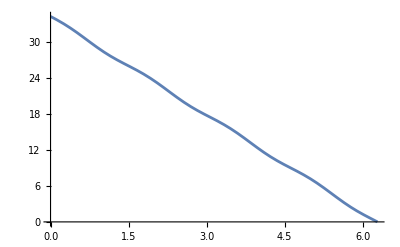

```mathematica
Plot[f[1, 0,1,theta, phi,1, .9,Pi/10,x],{x,0,2Pi}]
```

# Eigenvalue

```mathematica
lambda[t_, r_, theta_, phi_, M_, Ω_, v_]=Eigenvalues[ElectricQuadM[t,r,theta,phi,M,Ω]]
```

{-1/(8 √2 r)√(70+56 Cos[2 theta]+2 Cos[4 theta]+6 Cos[4 phi-4 (-r+t) Ω]+Cos[4 phi-4 theta-4 (-r+t) Ω]-4 Cos[4 phi-2 theta-4 (-r+t) Ω]-4 Cos[4 phi+2 theta-4 (-r+t) Ω]+Cos[4 phi+4 theta-4 (-r+t) Ω]) (M Ω^4+M r^4 Ω^4 Sin[theta]^2),1/(8 √2 r)√(70+56 Cos[2 theta]+2 Cos[4 theta]+6 Cos[4 phi-4 (-r+t) Ω]+Cos[4 phi-4 theta-4 (-r+t) Ω]-4 Cos[4 phi-2 theta-4 (-r+t) Ω]-4 Cos[4 phi+2 theta-4 (-r+t) Ω]+Cos[4 phi+4 theta-4 (-r+t) Ω]) (M Ω^4+M r^4 Ω^4 Sin[theta]^2)}

```mathematica
ElectricQuadM[t,r,theta,phi,M,Ω][[1]]
MagneticQuadM[t,r,theta,phi,M,Ω][[1]]
```

{-1/(2 r)(M Ω^4 (1+Cos[theta]^2) Cos[2 (phi-(-r+t) Ω)]+M r^4 Ω^4 (1+Cos[theta]^2) Cos[2 (phi-(-r+t) Ω)] Sin[theta]^2),-1/(2 r)(-2 M Ω^4 Cos[theta] Sin[2 (phi-(-r+t) Ω)]-2 M r^4 Ω^4 Cos[theta] Sin[theta]^2 Sin[2 (phi-(-r+t) Ω)])}

{-(2 M Ω^4 Cos[theta] √(r^4 Sin[theta]^2) Sin[2 (phi-(-r+t) Ω)])/r,-(M Ω^4 (1+Cos[theta]^2) Cos[2 (phi-(-r+t) Ω)] √(r^4 Sin[theta]^2))/r}